```mathematica
{FullForm[a*b+c],FullForm[a+b*c]}
```

{Plus[Times[a,b],c],Plus[a,Times[b,c]]}

```mathematica
a*b+c//f
```

f[a b+c]

```mathematica
f@a*b+c
```

c+b f[a]

```mathematica
FullForm[a*(b+c)]
```

Times[a,Plus[b,c]]

```mathematica
FullForm[%]
```

Times[a,Plus[b,c]]

```mathematica
{x->#^2&,(x->#^2)&,x->(#^2&)}
```

{x→#1^2&,x→#1^2&,x→(#1^2&)}

```mathematica
FullForm[a+b+c+d]
```

Plus[a,b,c,d]

```mathematica
FullForm[a^b^c^d]
```

Power[a,Power[b,Power[c,d]]]

```mathematica
a⊕b⊕c//FullForm
```

CirclePlus[a,b,c]

```mathematica
a*a*a*b*b*c
```

a^3 b^2 c

```mathematica
∫k[x] ⅆx//FullForm
```

Integrate[k[x],x]

```mathematica
∫a[x] b[x] ⅆx+c[x]
```

c[x]+∫a[x] b[x]ⅆx

```mathematica
∫(a[x]+b[x]) ⅆx+c[x]
```

c[x]+∫(a[x]+b[x])ⅆx

```mathematica
x^(a+b)
```

x^(a+b)

```mathematica
D[x^n, x]
```

n x^(-1+n)

```mathematica
∑_(n=1)^∞ 1/n^s
```

Zeta[s]

```mathematica
∑_(n=1)^∞ 1/n^s + n
```

n+Zeta[s]

```mathematica
1+2/3
```

5/3

```mathematica
(1+2)/3
```

1

```mathematica
{1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
{1,b,2,3,3 x==12,Sqrt[9+y],"hello"}
```

{1,b,2,3,3 x==12,√(9+y),hello}

```mathematica
{1,1,{3,4,5},{3,2}}
```

{1,1,{3,4,5},{3,2}}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
N[Sin[2]]
```

0.909297

```mathematica
v=Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
v[[3]]
```

9

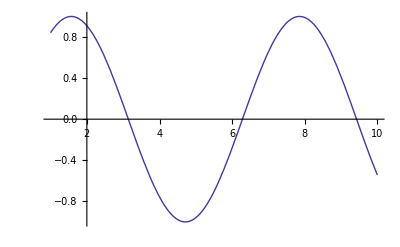

```mathematica
Plot[Sin[x],{x,1,10}]
```

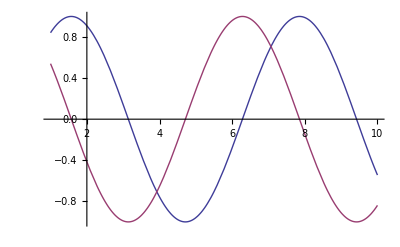

```mathematica
Plot[{Sin[x],Cos[x]},{x,1,10}]
```

```mathematica
3+62-1
```

64

```mathematica
3 x-x+2
```

2+2 x

```mathematica
-1+2 x+x^3
```

-1+2 x+x^3

```mathematica
x^2+x-4 x^2
```

x-3 x^2

```mathematica
x y+2 x^2 y+y^2 x^2-2 y x
```

-x y+2 x^2 y+x^2 y^2

```mathematica
(x+2 y+1) (x-2)^2
```

(-2+x)^2 (1+x+2 y)

```mathematica
Expand[%]
```

4-3 x^2+x^3+8 y-8 x y+2 x^2 y

```mathematica
Factor[%]
```

(-2+x)^2 (1+x+2 y)

```mathematica
Sqrt[2]/9801 (4 n)! (1103+26390 n)/(n!^4 396^(4 n))
```

(2^(1/2-8 n) 99^(-2-4 n) (1103+26390 n) (4 n)!)/(n!)^4

```mathematica
Sqrt[1+x]^4
```

(1+x)^2

```mathematica
Log[1+Cos[x]]
```

Log[1+Cos[x]]

```mathematica
1+2 x/.x->3
```

7

```mathematica
1+x+x^2/.x->2-y
```

3+(2-y)^2-y

```mathematica
(x+y) (x-y)^2/.{x->3,y->1-a}
```

(4-a) (2+a)^2

```mathematica
x=3
```

3

```mathematica
x^2-1
```

8

```mathematica
x=.
```

```mathematica
x+5-2 x
```

5-x

```mathematica
t=1+x^2
```

1+x^2

```mathematica
t/.x->2
```

5

```mathematica
t/.x->Pi//N
```

10.8696

```mathematica
Simplify[x^2+2 x+1]
```

(1+x)^2

```mathematica
Integrate[1/(x^4-1),x]
```

-ArcTan[x]/2+1/4 Log[1-x]-1/4 Log[1+x]

```mathematica
D[%,x]
```

-1/(4 (1-x))-1/(4 (1+x))-1/(2 (1+x^2))

```mathematica
Simplify[%]
```

1/(-1+x^4)

```mathematica
Simplify[Gamma[x] Gamma[1-x]]
```

Gamma[1-x] Gamma[x]

```mathematica
FullSimplify[Gamma[x] Gamma[1-x]]
```

π Csc[π x]

```mathematica
D[x^n,x]
```

n x^(-1+n)

```mathematica
D[x[1]^2+x[2]^2,x[1]]
```

2 x[1]

```mathematica
D[x^2+y^2,x]
```

2 x

```mathematica
D[x^2+y^2,x,NonConstants->{y}]
```

2 x+2 y D[y,x,NonConstants→{y}]

```mathematica
D[x^2+y^2,{{x,y}}]
```

{2 x,2 y}

```mathematica
D[x^2+y^2,{{x,y},2}]
```

{{2,0},{0,2}}

```mathematica
D[{x^2+y^2,x y},{{x,y}}]
```

{{2 x,2 y},{y,x}}

```mathematica
Integrate[1/(x^4-a^4),x]
```

-ArcTan[x/a]/(2 a^3)+Log[a-x]/(4 a^3)-Log[a+x]/(4 a^3)

```mathematica
Integrate[Sin[x^2],x]
```

√(π/2) FresnelS[√(2/π) x]

```mathematica
Integrate[x^x,x]
```

∫x^x ⅆx

```mathematica
Integrate[Sin[x]^2,{x,a,b}]
```

1/2 (-a+b+Cos[a] Sin[a]-Cos[b] Sin[b])

```mathematica
Integrate[Exp[-x^2],{x,0,Infinity}]
```

(√π)/2

```mathematica
Integrate[x^2+y^2,{x,0,1},{y,0,x}]
```

1/3

```mathematica
Integrate[x^10 Boole[x^2+y^2≤1],{x,-1,1},{y,-1,1}]
```

(21 π)/512

```mathematica
Integrate[x^2,x]
```

x^3/3

```mathematica
D[%+c,x]
```

x^2

```mathematica
Integrate[1/(1-b x^2),x]
```

ArcTanh[√b x]/(√b)

```mathematica
%/.b->-a
```

ArcTanh[√-a x]/(√-a)

```mathematica
D[%,x]
```

1/(1+a x^2)

```mathematica
Simplify[D[{ArcTan[x],-ArcTan[1/x]},x]]
```

{1/(1+x^2),1/(1+x^2)}

```mathematica
Integrate[1/(1+x^2),x]
```

ArcTan[x]

```mathematica
DSolve[y'[x]+y[x]==1,y[x],x]
```

{{y[x]→1+ⅇ^-x C[1]}}

```mathematica
y[x]+2 y'[x]+y[0]/.%
```

{1+ⅇ^-x C[1]+y[0]+2 y'[x]}

```mathematica
y'[x]+y[x]==1/.%%
```

{1+ⅇ^-x C[1]+y'[x]==1}

```mathematica
DSolve[{y[x]==-z'[x],z[x]==-y'[x]},{y,z},x]
```

{{y→Function[{x},1/2 ⅇ^-x (1+ⅇ^(2 x)) C[1]-1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[2]],z→Function[{x},-1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[1]+1/2 ⅇ^-x (1+ⅇ^(2 x)) C[2]]}}

```mathematica
DSolve[y[x] y'[x]==1,y,x]
```

{{y→Function[{x},-√2 √(x+C[1])]},{y→Function[{x},√2 √(x+C[1])]}}

```mathematica
DSolve[{y'[x]==a y[x],y[0]==1},y[x],x]
```

{{y[x]→ⅇ^(a x)}}

```mathematica
DSolve[y''[x]-Exp[x] y[x]==0,y[x],x]
```

{{y[x]→BesselI[0,2 √(ⅇ^x)] C[1]+2 BesselK[0,2 √(ⅇ^x)] C[2]}}

```mathematica
DSolve[y'[x]-y[x]^2==0,y[x],x]
```

{{y[x]→1/(-x-C[1])}}

```mathematica
DSolve[y'[x]-y[x]^2==x,y[x],x]//FullSimplify
```

{{y[x]→(√x (-BesselJ[-2/3,(2 x^(3/2))/3]+BesselJ[2/3,(2 x^(3/2))/3] C[1]))/(BesselJ[1/3,(2 x^(3/2))/3]+BesselJ[-1/3,(2 x^(3/2))/3] C[1])}}

```mathematica
DSolve[x1 D[y[x1,x2],x1]+x2 D[y[x1,x2],x2]==Exp[x1 x2],y[x1,x2],{x1,x2}]
```

{{y[x1,x2]→1/2 (ExpIntegralEi[x1 x2]+2 C[1][x2/x1])}}

```mathematica
DSolve[D[y[x1,x2],x1] D[y[x1,x2],x2]==a,y[x1,x2],{x1,x2}]
```

DSolve::nlpde: Solution requested to nonlinear partial differential equation. Trying to build a special solution.

{{y[x1,x2]→C[1]+(a x1)/C[2]+x2 C[2]}}

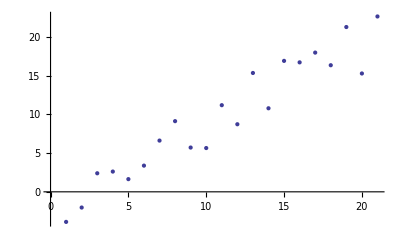

```mathematica
datapts=Table[x+RandomReal[{-4,4}],{x,0,20}];
ListPlot[datapts]
```

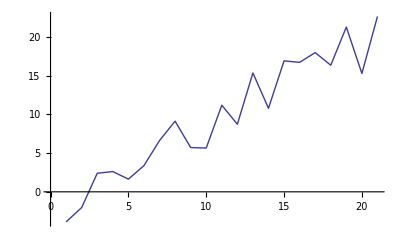

```mathematica
ListLinePlot[datapts]
```